# M5: Hooke’s Law and the Simple Harmonic Oscillator

## Calvin Zikakis Section 311 Drew Morrill April 18th, 2017

## Introduction

In this lab, we used Hooke’s Law which allowed us to calculate the spring constant (k) by using force applied onto the spring. We also explored the effects of simple harmonic motion, which occurs whenever there is a restoring force proportional to the displacement from equilibrium. In order to achieve these calculations, we used various hanging weights attached to springs to measure the spring constant, k. We measured the period of oscillation of all of the various masses hanging on the springs. This lab allowed us to better understand the concepts of simple harmonic motion and Hooke’s law, two important aspects of physics.

## Part 1: Measurement of the Spring Constant k

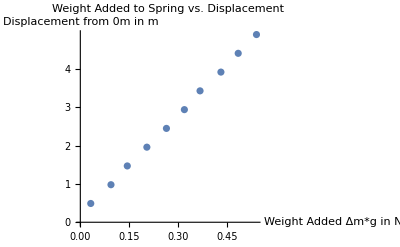

```mathematica
mspring = 0.1605; (*Mass of Spring in kg*)
δmspring = 0.0001 ;(*Uncertianty in the Spring's Mass in kg*)

m = {0.050,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5}; (*Added mass in kg*)
d = {0.243,0.305,0.355,0.415,0.475,0.530,0.578,0.642,0.695,0.751};(*Measured Displacement in m*)

dact = d-0.211; (*Displacement from 0 m in m*)
weight = m*9.786; (*Weight addaed to Spring in N*)

weightdata = Thread[{dact,weight}];
ListPlot[weightdata,PlotLabel-> "Weight Added to Spring vs. Displacement",AxesLabel-> {"Weight Added Δm*g in N","Displacement from 0m in m"}]
```

The masses look like they perfectly correspond with our collected displacements. There seems to be no random error in my graph. My graph should look like a linear function as it does due to Hooke’s law being a linear function. There is not enough data to tell if there was a systematic error, but by looking at the graph we can see that the data was relatively accurate. The slope of this line should be our spring constant.

```mathematica
kdata = weight/dact (*List of k Values*)

kavg =( ∑_(i=1)^Length[kdata] kdata[[i]])/Length[kdata] (*Average Value of k in N/m*)
ksd = √((∑_(i=1)^Length[kdata] (kdata[[i]]-kavg)^2)/(Length[kdata]-1));(*Standard Deviation of k in N/m*)
ksdom = ksd/√Length[kdata](*Standard on the Mean of k in N/m*)
```

{15.2906,10.4106,10.1938,9.59412,9.26705,9.20313,9.3327,9.08213,9.09855,9.06111}

10.0534

0.600807

Using my data from the calculations would give us a K value of (10.1  ±  0.6) N/m. The error on this value seems a bit high, but overall I would conclude that this value is relatively accurate. Without any known value to compare my result to, we have to conclude this result is reasonable. This high error is most-likely systematic due to human error on measuring the distance the spring has fallen. The length function used in the code above computes the amount of data points in an array.

## Part 2: Measurement of the Period

```mathematica
m2 = {0.1,0.2,0.3}; (*Hooked Masses Mass in kg*)
Tavg = {0.8208,1.0338,1.2246}; (*Average Period of 50 Oscillations in s*)

meff = m2+(0.281*mspring); (*Effective Mass in kg*)

Tcalc = 2π √(meff/kavg) (*Calculated Period in s*)
δTcalc = Tcalc[[1]] √((1/2*0.0001/meff[[1]])^2+(1/2*ksdom/kavg)^2)(*Uncertianty on T for the first point in s*)
δTcalc = Tcalc[[1]] √((1/2*0.0001/meff[[2]])^2+(1/2*ksdom/kavg)^2)(*Uncertianty on T for the second point in s*)
δTcalc = Tcalc[[1]] √((1/2*0.0001/meff[[3]])^2+(1/2*ksdom/kavg)^2)(*Uncertianty on T for the third point in s*)
```

{0.754846,0.981061,1.16412}

0.0225569

0.022556

0.0225557

For the 100g mass, the calculated period is (0.76 ± 0.02) s.
For the 200g mass, the calculated period is (0.98 ± 0.02) s.
For the 300g mass, the calculated period is (1.16 ± 0.02) s.

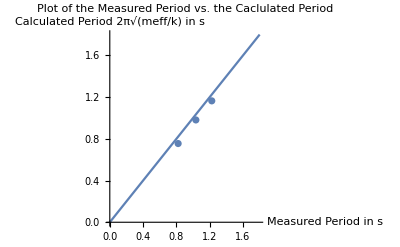

{1.08737,1.05376,1.05196}

```mathematica
Tdata = Thread[{Tavg,Tcalc}];
TPlot = Show[Plot[x,{x,0,1.8}],ListPlot[Tdata],PlotLabel-> "Plot of the Measured Period vs. the Caclulated Period",AxesLabel->{"Measured Period in s","Calculated Period 2π√(meff/k) in s"}]
Rvalue = Tavg/Tcalc
```

This graph shows the relationship between measured and calculated period. The line seems to fit my data well but with a small amount of systematic error that can be seen by the points laying slightly under the line. This error could be from a number of things, but most-likely it stems from timing error. The Rvalue is the ratio of recorded value to calculated value. The further the Rvalue is from 1, the worse the data is. My data points all have Rvalues relatively close to one meaning all of the values are close to the actual values.

## Conclusion

In conclusion, this lab helped our understanding of simple harmonic motion and Hooke’s law of a spring. By measuring the displaced distance of the spring when applying various masses, we were able to use our data to calculate the spring constant, “k”. Then we ere able to use the k values we calculated to find theoretical periods for the spring and varying mass system. These calculations helped to check that our observations of average periods were in fact correct. My data returned a systematic error of my measured points being lower than my theoretical line. I believe this error was due to the relatively high error in the initial calculation of my spring constant, “k”. If my measured spring constant data was better, I assume that my data points would have fallen perfectly on the line. Overall, this systematic error was the only major error in my data.